```mathematica
Вариант 8;
```

```mathematica
1.Задаем начальные данные;
```

```mathematica
Subscript[x, 0]=0.1; Subscript[x, 1]=0.3; Subscript[x, 2]=0.7;Subscript[x, 3]=1.4;
Subscript[f, 0]=1; Subscript[f, 1]=-7; Subscript[f, 2]=15;Subscript[f, 3]=25;
n = 3;
```

```mathematica
2. Формируем линейный интерполяционный сплайн на частичном отрезке [Subscript[x, k],Subscript[x, k+1]];
```

```mathematica
Subscript[P, k_][t_]=Subscript[f, k]+(t-Subscript[x, k])*Subscript[A, k];
```

```mathematica
3. Записываем интерполяционные условия в систему линейных уравнений;
```

```mathematica
eq1=Table[Subscript[P, k][Subscript[x, k+1]]==Subscript[P, k+1][Subscript[x, k+1]],{k,0,n-2}];
eq2={Subscript[P, n-1][Subscript[x, n]]==Subscript[f, n]};
```

```mathematica
4. Формируем систему линейных уравнений
для определения неизвестных коэффициентов сплайна;
```

4. систему линейных Формируем уравнений

```mathematica
eq=Join[eq1,eq2]
```

{1+0.2 A_0==-7.,-7+0.4 A_1==15.,15+0.7 A_2==25}

```mathematica
5. Решаем систему линейных уравнений;
```

```mathematica
koef=Solve[eq,{}]
```

{{A_0→-40.,A_1→55.,A_2→14.2857}}

```mathematica
6. Строим искомый сплайн;
```

```mathematica
spl=Table[Subscript[P, k][t]/.koef,{k,0,n-1}]//Expand//Flatten
```

{5.-40. t,-23.5+55. t,5.+14.2857 t}

```mathematica
8. Проверяем интерполяционные условия;
```

```mathematica
Table[(spl[[k]]//.t->Subscript[x, k-1])==Subscript[f, k-1],{k,1,n}]
(spl[[n]]//.t->Subscript[x, n])==Subscript[f, n]
```

{True,True,True}

True

```mathematica
10. Изображаем исходную систему точек и
полученный интерполяционный сплайн в одной системе координат;
```

10. и точек систему исходную Изображаем

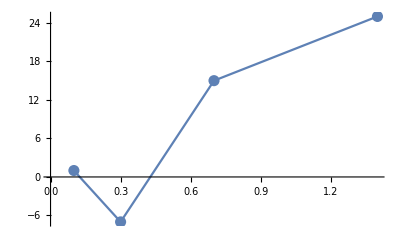

```mathematica
Gr1=ListPlot[Table[{Subscript[x, i],Subscript[f, i]},{i,0,n}],PlotStyle->{PointSize[0.02]}];
Gr2=Table[Plot[spl[[k]],{t,Subscript[x, k-1],Subscript[x, k]}],{k,1,n}];Show[Gr1,Gr2]
```

```mathematica
a=Subscript[x, 0]=0.1; Subscript[x, 1]=0.3; Subscript[x, 2]=0.7;Subscript[x, 3]=1.4;
Subscript[f, 0]=1; Subscript[f, 1]=-7; Subscript[f, 2]=15;Subscript[f, 3]=25;
n = 3;
```

```mathematica
Subscript[P, k_][t_]=Subscript[f, k]+(t-Subscript[x, k])*(Subscript[A, k] t+Subscript[B, k]);
```

```mathematica
eq1=Table[Subscript[P, k][Subscript[x, k+1]]==Subscript[P, k+1][Subscript[x, k+1]],{k,0,n-2}];
Subscript[PP, k_][t_]=D[Subscript[P, k][t], t];
eq2=Table[Subscript[PP, k][Subscript[x, k+1]]==Subscript[PP, k+1][Subscript[x, k+1]],{k,0,n-2}];
eq3={Subscript[P, n-1][Subscript[x, n]]==Subscript[f, n]};
```

```mathematica
eq4={Subscript[PP, 0][a]==0};
```

```mathematica
eq=Join[eq1,eq2,eq3,eq4]
```

{1+0.2 (0.3 A_0+B_0)==-7.,-7+0.4 (0.7 A_1+B_1)==15.,0.5 A_0+B_0==0.+0.3 A_1+B_1,1.1 A_1+B_1==0.+0.7 A_2+B_2,15+0.7 (1.4 A_2+B_2)==25,0.+0.1 A_0+B_0==0}

```mathematica
koef=Solve[eq,{}]
```

{{A_0→-200.,A_1→337.5,A_2→-251.02,B_0→20.,B_1→-181.25,B_2→365.714}}

```mathematica
spl=Table[Subscript[P, k][t]/.koef,{k,0,n-1}]//Expand//Flatten
```

{-1.+40. t-200. t^2,47.375-282.5 t+337.5 t^2,-241.+541.429 t-251.02 t^2}

```mathematica
Table[(spl[[k]]//.t->Subscript[x, k-1])==Subscript[f, k-1],{k,1,n}]
(spl[[n]]//.t->Subscript[x, n])==Subscript[f, n]
```

{True,True,True}

True

```mathematica
(D[spl[[1]],{t,1}]//.t->a)==0
```

True

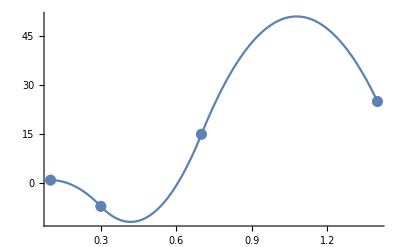

```mathematica
Gr1=ListPlot[Table[{Subscript[x, i],Subscript[f, i]},{i,0,n}],PlotStyle->{PointSize[0.02]}];
Gr3=Table[Plot[spl[[k]],{t,Subscript[x, k-1],Subscript[x, k]}],{k,1,n}];Show[Gr1,Gr3,PlotRange->All]
```

```mathematica
a=Subscript[x, 0]=1/10; Subscript[x, 1]=3/10; Subscript[x, 2]=7/10;b=Subscript[x, 3]=14/10;
Subscript[f, 0]=1; Subscript[f, 1]=-7; Subscript[f, 2]=15;Subscript[f, 3]=25;
n = 3;
```

```mathematica
Subscript[P, k_][t_]=Subscript[f, k]+(t-Subscript[x, k])*(Subscript[A, k] t^2+Subscript[B, k] t+Subscript[C, k]);
```

```mathematica
eq1=Table[Subscript[P, k][Subscript[x, k+1]]==Subscript[P, k+1][Subscript[x, k+1]],{k,0,n-2}];
Subscript[PP, k_][t_]=D[Subscript[P, k][t], t];
eq2=Table[Subscript[PP, k][Subscript[x, k+1]]==Subscript[PP, k+1][Subscript[x, k+1]],{k,0,n-2}];
Subscript[PPP, k_][t_]=D[Subscript[PP, k][t], t]; 
eq3=Table[Subscript[PPP, k][Subscript[x, k+1]]==Subscript[PPP, k+1][Subscript[x, k+1]],{k,0,n-2}];
eq4={Subscript[P, n-1][Subscript[x, n]]==Subscript[f, n]};
```

```mathematica
eq6={Subscript[PPP, n-1][Subscript[x, n]]==0};
eq5={Subscript[PPP, 0][Subscript[x, 0]]==0};
```

```mathematica
eq=Join[eq1,eq2,eq3,eq4,eq5,eq6]
```

{1+1/5 ((9 A_0)/100+(3 B_0)/10+C_0)==-7,-7+2/5 ((49 A_1)/100+(7 B_1)/10+C_1)==15,(9 A_0)/100+(3 B_0)/10+1/5 ((3 A_0)/5+B_0)+C_0==(9 A_1)/100+(3 B_1)/10+C_1,(49 A_1)/100+(7 B_1)/10+2/5 ((7 A_1)/5+B_1)+C_1==(49 A_2)/100+(7 B_2)/10+C_2,(8 A_0)/5+2 B_0==(6 A_1)/5+2 B_1,(18 A_1)/5+2 B_1==(14 A_2)/5+2 B_2,15+7/10 ((49 A_2)/25+(7 B_2)/5+C_2)==25,(2 A_0)/5+2 B_0==0,7 A_2+2 B_2==0}

```mathematica
koef=Solve[eq,{}]
```

{{A_0→197125/434,A_1→-273125/868,A_2→76000/1519,B_0→-39425/434,B_1→400425/868,B_2→-38000/217,C_0→-93095/1736,C_1→-56415/496,C_2→35020/217}}

```mathematica
spl=Table[Subscript[P, k][t]/.koef,{k,0,n-1}]//Expand//Flatten
```

{22091/3472-(77325 t)/1736-(118275 t^2)/868+(197125 t^3)/434,26905/992-(875415 t)/3472+(964725 t^2)/1736-(273125 t^3)/868,-3037/31+(61620 t)/217-(45600 t^2)/217+(76000 t^3)/1519}

```mathematica
Table[(spl[[k]]//.t->Subscript[x, k-1])==Subscript[f, k-1],{k,1,n}]
(spl[[n]]//.t->Subscript[x, n])==Subscript[f, n]
```

{True,True,True}

True

```mathematica
(D[spl[[1]],{t,2}]//.t->a)==0
(D[spl[[n]],{t,2}]//.t->b)==0
```

True

True

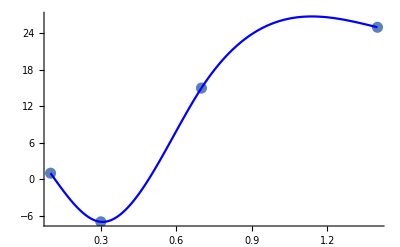

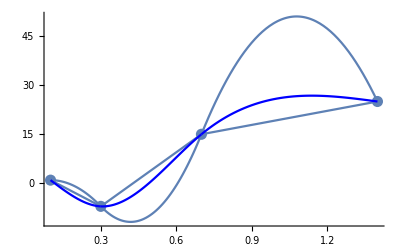

```mathematica
Gr1=ListPlot[Table[{Subscript[x, i],Subscript[f, i]},{i,0,n}],PlotStyle->{PointSize[0.02]}];
Gr4=Table[Plot[spl[[k]],{t,Subscript[x, k-1],Subscript[x, k]},PlotStyle->{Red,Blue}],{k,1,n}];
Show[Gr1,Gr4,PlotRange->All]
Show[Gr1,Gr2,Gr3,Gr4,PlotRange->All]
```